## 变化

## 最优停止问题

### 蒙特卡洛模拟

```mathematica
MonteCarloSimulation[k_,n_]:=Module[{candidates,bestInFirstHalf,selected},candidates=RandomSample[Range[n]];
bestInFirstHalf=Max[Take[candidates,k]];
selected=FirstCase[Drop[candidates,k],x_/;x>bestInFirstHalf,0];
selected==Max[candidates]]
OptimalStoppingProbability[k_,n_,iterations_]:=N[Count[Table[MonteCarloSimulation[k,n],iterations],True]/iterations]
```

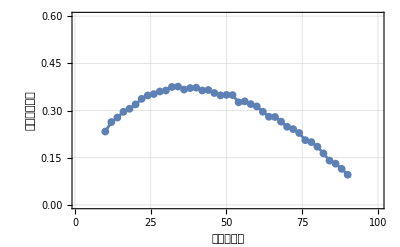

```mathematica
ListLinePlot[Table[{i,OptimalStoppingProbability[i,100,10000]},{i,10,90,2}],PlotTheme->"Detailed",PlotLegends->None,FrameLabel->{"上半场人数","最佳选择概率"},PlotMarkers->{Automatic, 8},PlotRange->{{1,100},{0,.6}}]
```

### 小人数的37%法则

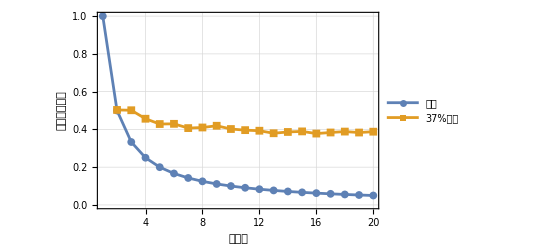

```mathematica
ListLinePlot[{Table[{i,1/i},{i,1,20}],Table[{i,OptimalStoppingProbability[Round[.37 i],i,10000]},{i,2,20}]},PlotTheme->"Detailed",PlotLegends->{"盲选","37%法则"},FrameLabel->{"总人数","最佳选择概率"},PlotMarkers->{Automatic, 8},PlotRange->{{1,20},{0,1}}]
```

## 相交区域的体积

```mathematica
cy1=Cylinder[{{0,0,-5},{0,0,5}},1];
cy2=Cylinder[{{-5,0,0},{5,0,0}},1];
region=RegionIntersection[cy1,cy2];
#@region&/@{Volume,Region}
```

{16/3,-Graphics3D-}